## SFH 4550

FittedModel[…]

{Rs→0.901735,N→1.79103,Is→2.47116×10^-15}

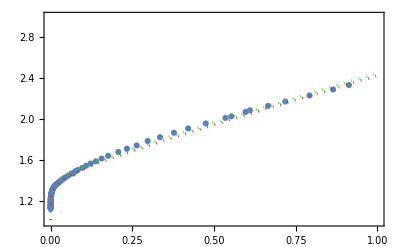

```mathematica
Clear["`*"]
(*Temperature*)
kB=QuantityMagnitude[Quantity["BoltzmannConstant"],"Joules"/"Kelvins"];
e=QuantityMagnitude[Quantity["ElementaryCharge"],"Coulombs"];
Tcelsius=25;
Tkelvin=Tcelsius+273.15;
Vt=(kB Tkelvin)/e;

(*data -- (ID, VD)*)
data=Rest[Import["/mnt/c/Users/micha/Desktop/IR-Headset/Diode Data/SFH 4550.csv"]];
data=data/. {VD_,ID_}->{ID,VD};

(*Model Manually Set*)
RsMan=0.9;
NMan=1.7;
IsMan=7*^-16;
VDMan[ID_]:=RsMan ID+NMan Vt Log[ID/IsMan+1];

(*Model Fitted*)
VDFit[ID_]:=Rs ID+N Vt Log[ID/Is+1];
nlm=NonlinearModelFit[data, VDFit[ID],{{Rs,0.01},{N,1},{Is,1 10^-20}},ID]
nlm["BestFitParameters"]

(*Plot*)
Show[ListPlot[data],Plot[nlm[ID],{ID,0.00001,1},PlotStyle->{Dotted,Green}],Plot[VDMan[ID],{ID,0.00001,1},PlotStyle->{Dotted,Red}],Frame->True,PlotRange->{{0,1},{1,3}}]
```

## BF5H06H-YIR-050

Divide::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::nrjnum: The Jacobian is not a matrix of real numbers at {Rs,N,Is} = {2.7,0.102,1.×10^-219}.

FittedModel[…]

{Rs→2.7,N→0.102,Is→1.×10^-219}

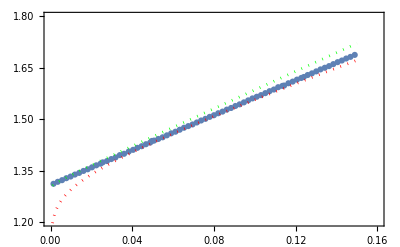

```mathematica
Clear["`*"]
(*Temperature*)
kB=QuantityMagnitude[Quantity["BoltzmannConstant"],"Joules"/"Kelvins"];
e=QuantityMagnitude[Quantity["ElementaryCharge"],"Coulombs"];
Tcelsius=25;
Tkelvin=Tcelsius+273.15;
Vt=(kB Tkelvin)/e;

(*data -- (ID, VD)*)
data=Rest[Import["/mnt/c/Users/micha/Desktop/IR-Headset/Diode Data/BF5H06H-YIR-050.csv"]];
data=data/. {VD_,ID_}->{ID,VD};

(*Model Manually Set*)
RsMan=2.03;
NMan=1.346;
IsMan=1*^-18;
VDMan[ID_]:=RsMan ID+NMan Vt Log[ID/IsMan+1];

(*Model Fitted*)
VDFit[ID_]:=Rs ID+N Vt Log[ID/Is+1];
nlm=NonlinearModelFit[data,VDFit[ID],{{Rs,2.7},{N,0.102},{Is,1*10^-219}},ID]
nlm["BestFitParameters"]

(*Plot*)
Show[ListPlot[data],Plot[nlm[ID],{ID,0.001,0.15},PlotStyle->{Dotted,Green}],Plot[VDMan[ID],{ID,0.001,0.15},PlotStyle->{Dotted,Red}],Frame->True,PlotRange->{{0,0.160},{1.2,1.8}}]
```